# Mathematica入门

## 高家鹏 华中科技大学物理学院

## 基本知识

我们一般的工作界面就是笔记本界面，运算是用各种各样的函数来进行的
函数的表示方法是Sin[ ]这样的形式，在方括号里面输入适当的内容，然后按shift+enter就可以得到运算结果
若要终止运算，按alt+,



```mathematica
Plot[Sin[x],{x,0,10}]
```

## 关于输入

快捷键

```mathematica
2^2,1/2
```

希腊字母，自然常数，奇奇怪怪的符号等等的输入esc+单词/字母+esc

```mathematica
θ,ω,♔
```

使用面板中的“数学助手”可以解决绝大部分输入问题

## 特殊符号

比如说自然常数、π等等符号，他们的含义是不能随便更改的

```mathematica
Pi//N
```

```mathematica
E//N
```

```mathematica
I
```

```mathematica
Infinity
```

## 算术运算

```mathematica
2^(1/2)
```

```mathematica
2^(1/2)//N
```

```mathematica
N[2^(1/2),10]
```

```mathematica
Sin[1]//N
```

## 代数运算

不用声明变量，不用赋值，可以直接进行符号运算

```mathematica
Simplify[(x^2+2x+1)/(x+1)]
```

```mathematica
Expand[(1+x)^100]
```

```mathematica
Simplify[Cos[n*Pi],n∈Integers]
```

```mathematica
a=4
```

```mathematica
a+2==6
```

```mathematica
Solve[x^3+x^2+x==b]
```

```mathematica
{{b->x (1+x+x^2)}}/.{x->2}
```

## 局部变量与清除变量

概念类似于C++中的局部变量

```mathematica
x=1;
Module[{x},
x=2;
x
]
x
```

```mathematica
Clear["Global`*"]
```

```mathematica
x
```

```mathematica
x=1;
x
x=.;
x
```

## 微积分

导数/偏导

```mathematica
D[ArcTan[x],x]
```

```mathematica
D[Sin[n*x],x]
```

```mathematica
D[Sin[n*x],{x,4}]
```

全微分

```mathematica
Dt[x^n,x]
```

积分

```mathematica
Integrate[1/x,x]
```

```mathematica
Integrate[x^x,{x,0,10}]
```

```mathematica
Integrate[1/x,{x,1,2}]
```

```mathematica
NIntegrate[x^x,{x,0,10}]
```

```mathematica
∑_(n=0)^Infinity x^n/n!
```

```mathematica
Limit[Sin[x]/x,x->0]
```

```mathematica
Series[Sin[x],{x,0,10}]
```

```mathematica
DSolve[{D[x[t],t]==3*x[t],x[0]==1},x,t]
```

## 自定义函数

```mathematica
f[x_]:=Integrate[Exp[-t]*x,{t,0,10}];
f[Sin[t]]
```

1/2-(Cos[10]+Sin[10])/(2 ⅇ^10)

## 列表操作

列表在Mathematica中可以作为数组，也可以作为向量和矩阵使用

```mathematica
a={1,2,3,4,5};
a[[1]]
```

1

```mathematica
a={{1,2,3},{4,5,6},{7,8,9}};
a[[3]]
```

{7,8,9}

```mathematica
a[[1;;2]]
```

{{1,2},{4,5}}

```mathematica
a[[1;;2,1;;2]]
```

{{1,2},{4,5}}

```mathematica
b={{23,435,13}};
Join[a,b]
```

{{1,2,3},{4,5,6},{7,8,9},{23,435,13}}

```mathematica
va={a1,a2,a3};
vb={b1,b2,b3};
va.vb
va×vb
```

a1 b1+a2 b2+a3 b3

{-a3 b2+a2 b3,a3 b1-a1 b3,-a2 b1+a1 b2}

```mathematica
ma={{a11,a12,a13},{a21,a22,a23},{a31,a32,a33}};
mb={{b11,b12,b13},{b21,b22,b23},{b31,b32,b33}};
MatrixForm[ma.mb]
MatrixForm[ma.va]
```

```mathematica
la=Table[1/n,{n,1,10}]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10}

```mathematica
AppendTo[la,1]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1}

## 绘图

mma的绘图功能非常强大，可以画出2D 3D的各种类型图像，而且能在图像中插入各种图形

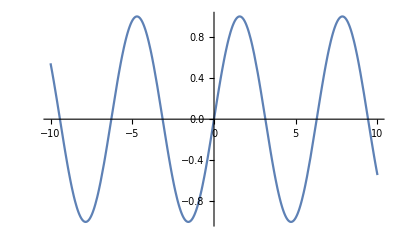

```mathematica
Plot[Sin[x],{x,-10,10}]
```

```mathematica
Plot3D[1Sin[x^2+y^2],{x,-5,5},{y,-5,5},MaxRecursion->6]
```

-Graphics3D-

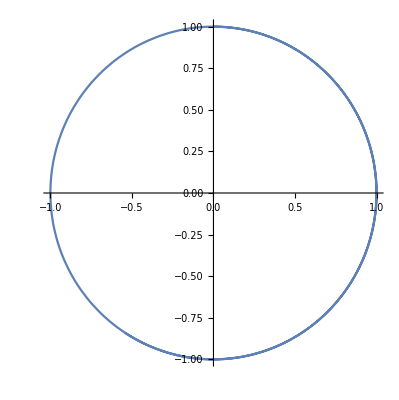

```mathematica
ParametricPlot[{Sin[t],Cos[t]},{t,0,10}]
```

```mathematica
ParametricPlot3D[{10Sin[t],10Cos[t],t},{t,0,100}]
```

-Graphics3D-

```mathematica
Show[Graphics3D[Sphere[{0,0,5},10]],ParametricPlot3D[{10Sin[t],10Cos[t],t},{t,0,100}]]
```

-Graphics3D-

## 交互式操作与动画

Mathematica可以制作一些简单的随数个参量变化的动画

```mathematica
Manipulate[Plot[Sin[x(1+a x)],{x,0,6}],{a,0,2}]
```

```mathematica
Animate[Plot[Sin[x+a],{x,0,10}],{a,0,5},AnimationRunning->False]
```

## 综合案例1：三体

```mathematica
Clear["Global`*"]
eqns={
m1*x1''[t]==(G*m1*m2/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2+(z2[t]-z1[t])^2))*(x2[t]-x1[t])/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2+(z2[t]-z1[t])^2)^0.5+(G*m1*m3/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2+(z3[t]-z1[t])^2))*(x3[t]-x1[t])/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2+(z3[t]-z1[t])^2)^0.5,

m1*y1''[t]==(G*m1*m2/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2)+(z2[t]-z1[t])^2)*(y2[t]-y1[t])/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2+(z2[t]-z1[t])^2)^0.5+(G*m1*m3/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2+(z3[t]-z1[t])^2))*(y3[t]-y1[t])/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2+(z3[t]-z1[t])^2)^0.5,

m1*z1''[t]==(G*m1*m2/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2)+(z2[t]-z1[t])^2)*(z2[t]-z1[t])/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2+(z2[t]-z1[t])^2)^0.5+(G*m1*m3/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2+(z3[t]-z1[t])^2))*(z3[t]-z1[t])/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2+(z3[t]-z1[t])^2)^0.5,

m2*x2''[t]==(G*m1*m2/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2+(z2[t]-z1[t])^2))*(x1[t]-x2[t])/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2+(z2[t]-z1[t])^2)^0.5+(G*m2*m3/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2+(z3[t]-z2[t])^2))*(x3[t]-x2[t])/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2+(z3[t]-z2[t])^2)^0.5,

m2*y2''[t]==(G*m1*m2/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2+(z2[t]-z1[t])^2))*(y1[t]-y2[t])/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2+(z2[t]-z1[t])^2)^0.5+(G*m2*m3/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2+(z3[t]-z2[t])^2))*(y3[t]-y2[t])/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2+(z3[t]-z2[t])^2)^0.5,

m2*z2''[t]==(G*m1*m2/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2+(z2[t]-z1[t])^2))*(z1[t]-z2[t])/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2+(z2[t]-z1[t])^2)^0.5+(G*m2*m3/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2+(z3[t]-z2[t])^2))*(z3[t]-z2[t])/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2+(z3[t]-z2[t])^2)^0.5,

m3*x3''[t]==(G*m1*m3/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2+(z3[t]-z1[t])^2))*(x1[t]-x3[t])/((x1[t]-x3[t])^2+(y3[t]-y1[t])^2+(z3[t]-z1[t])^2)^0.5+(G*m2*m3/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2+(z3[t]-z2[t])^2))*(x2[t]-x3[t])/((x2[t]-x3[t])^2+(y3[t]-y2[t])^2+(z3[t]-z2[t])^2)^0.5,

m3*y3''[t]==(G*m1*m3/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2+(z3[t]-z1[t])^2))*(y1[t]-y3[t])/((x1[t]-x3[t])^2+(y3[t]-y1[t])^2+(z3[t]-z1[t])^2)^0.5+(G*m2*m3/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2+(z3[t]-z2[t])^2))*(y2[t]-y3[t])/((x2[t]-x3[t])^2+(y3[t]-y2[t])^2+(z3[t]-z2[t])^2)^0.5,

m3*z3''[t]==(G*m1*m3/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2+(z3[t]-z1[t])^2))*(z1[t]-z3[t])/((x1[t]-x3[t])^2+(y3[t]-y1[t])^2+(z3[t]-z1[t])^2)^0.5+(G*m2*m3/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2+(z3[t]-z2[t])^2))*(z2[t]-z3[t])/((x2[t]-x3[t])^2+(y3[t]-y2[t])^2+(z3[t]-z2[t])^2)^0.5
};
params={G->6.67408*10^(-11),m1->100000000000000000,m2->100000000000000000,m3->100000000000000000};
ics={x1[0]==-8000/√3,y1[0]==0,z1[0]==0,x1'[0]==-20,y1'[0]==1,z1'[0]==-7,x2[0]==0,y2[0]==8000,z2[0]==0,x2'[0]==10,y2'[0]==0,z2'[0]==-5,x3[0]==8000/√3,y3[0]==0,z3[0]==0,x3'[0]==10,y3'[0]==0,z3'[0]==10};
soldp=First[NDSolve[{ics,eqns}/.params,{x1,y1,z1,x2,y2,z2,x3,y3,z3},{t,0,8000},Method->{"IndexReduction"->Automatic}]];
Animate[Graphics3D[{{{Red,Sphere[{x1[t],y1[t],z1[t]},1000]},{Blue,Sphere[{x2[t],y2[t],z2[t]},1000]},{Green,Sphere[{x3[t],y3[t],z3[t]},1000]}}/.soldp,{Red,Line[Map[Function[Evaluate[{x1[#],y1[#],z1[#]}/.soldp]],Range[0,t,10]]]},{Blue,Line[Map[Function[Evaluate[{x2[#],y2[#],z2[#]}/.soldp]],Range[0,t,10]]]},{Green,Line[Map[Function[Evaluate[{x3[#],y3[#],z3[#]}/.soldp]],Range[0,t,10]]]}},PlotRange->{{-30000,30000},{-30000,30000},{-30000,30000}},Axes->True,Ticks->True,ImageSize->500],{t,0,8000,10},SaveDefinitions->True]
```

## 资料

Mathematica自带帮助文件
Mathematica线上文档（中文版）
http://reference.wolfram.com/language/
《Mathematica与大学物理计算》（清华大学出版社）
《Mathematica全书》(Stephen Wolfram亲自编写)